```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)(*Norming constant problem*)
```

```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`mySGlab`;
```

```mathematica
(*Solving u_tt-u_xx+sin u=0    lab coord *)
```

## Exact solution

```mathematica
(*"1 soliton" solution from wiki, kink solution*)
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol1[x_,t_]:=4*ArcTan[Exp[pm*x-Sqrt[pm^2-1]*t]];(*kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol1[x,t],t,t]-D[sol1[x,t],x,x]+Sin[sol1[x,t]]]
Manipulate[Plot[sol1[x,t],{x,-10,10},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol2[x_,t_]:=4*ArcTan[Exp[pm*(x+t)-Sqrt[pm^2-1]*(x-t)]];(*kink sol for uxt=sin u*)
FullSimplify[D[sol2[x,t],x,t]-Sin[sol2[x,t]]]
Manipulate[Plot[sol2[x,t],{x,-50,50},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(t)]*Sech[pb*(x)]];(* sitting breather sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(x-t)]*Sech[pb*(x+t)]];(* moving breather sol for uxt=sin u*)
FullSimplify[D[sol3[x,t],x,t]-Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
eta=1/2;
sol4[x_,t_]:=4*ArcTan[Exp[(eta/2+1/2/eta)*x+(eta/2-1/2/eta)*t]];(* kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol4[x,t],t,t]-D[sol4[x,t],x,x]+Sin[sol4[x,t]]]
Manipulate[Plot[sol4[x,t],{x,-20,20},PlotRange->{-1,8}],{t,-10,10}]
```

0

```mathematica
theta=Pi/2-0.5;
eta=Exp[I theta];
omega=-Re[eta];
sol5[x_,t_]:=4*ArcTan[Sqrt[(1-omega^2)/omega^2]*Cos[omega*(t)]*Sech[Sqrt[1-omega^2]*(x)]];(*sitting breather sol for utt-uxx+sin u=0*)
Manipulate[Plot[sol5[x,t],{x,-20,20},PlotRange->{-5,5}],{t,-5,50}]
```

```mathematica
D[sol5[x,t],t,t]-D[sol5[x,t],x,x]+Sin[sol5[x,t]]/.x->1/.t->10
```

-1.249×10^-16

```mathematica
(*Check Lax Pair*)
X[x_,t_,z_]:=({{-I z, -D[u[x,t],x]/2}, {D[u[x,t],x]/2, I z}});
```

```mathematica
T[x_,t_,z_]:=({{I*Cos[u[x,t]] /4/z, I*Sin[u[x,t]]/4/z}, {I*Sin[u[x,t]] /4/z, -I*Cos[u[x,t]] /4/z}});
```

```mathematica
D[X[x,t,z],t]-D[T[x,t,z],x]+X[x,t,z].T[x,t,z]-T[x,t,z].X[x,t,z]
```

{{0,1/2 Sin[u[x,t]]-1/2 u^(1,1)[x,t]},{-1/2 Sin[u[x,t]]+1/2 u^(1,1)[x,t],0}}

## Normal Reflection Coefficient

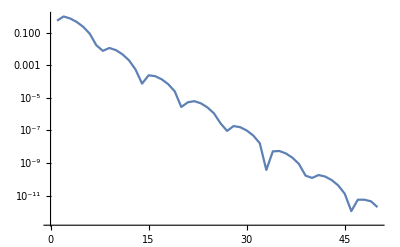
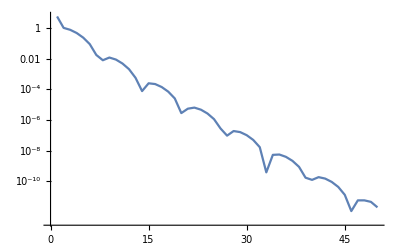
{0.0000149066,-Graphics-,-Graphics-}

```mathematica
eta=2;nc=4I;
sol3[x_,t_]:=4*ArcTan[nc/2/(I eta)*Exp[(eta/2+1/2/eta)*x+(eta/2-1/2/eta)*t]];
q[x_]:=sol3[x,0]/.Underflow[]->0/.Indeterminate->0.;
qt[x_]=D[sol3[x,t],t]/.t->0;
qx[x_]=D[sol3[x,t],x]/.t->0;
q[_?InfinityQ]:=0.;    (* PatternTest: q[infinity] gets replaces by 0 *)
qt[_?InfinityQ]:=0.;
LL=10;(*it seems this is related to the ill cond of H, but can we really evaluate H off real axis?*)
(*smaller LL H[0.01I] ill cond, but large LL H[10I] can be ill cond*)
H=ScatteringMatrixFiniteSG[q,qt,50,LL];
H[_?InfinityQ]=Sign[Re[H[1/0.0001I]]];;
H[_?PossibleZeroQ]=Sign[Re[H[0.0001I]]];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
```

```mathematica
Poles=LocatePolesSG[q,qx,qt,0.25,30]   (*why they are not the same as eta*)
```

{-7.28137×10^-16+2. ⅈ}

```mathematica
H[Poles[[1]]](*guess ill conditioning is due to evaluating abar in the upper half plane*)
```

{{1.90093×10^-8,1.},{1.,28.}}

```mathematica
ρ[k_]:=Piecewise[{{0,k==0},{bb[k]/aa[k],k!=0}}];
rad=0.2;
bigN=40;
SetParams[.4,rad,10.^(-6),20,bigN];
(*"SetParams[ν,rad,globalTol,smallN,bigN] sets the parameters for the rest of the code:
	ν: half of width of strip of analyticity
	rad: radius of soliton contours
	globalTol: contour truncation tolerance
	smallN: small number of collocation points
	bigN: big number of collocation points";if no truncations is done, then more points is required to get sufficient accuracy*)
ν=Getnu[];
h[k_]:=1/2/(1+Abs[k^2/2+1/3.2]^2);
Setrsamp[h];
Settimeflag[False];
c=SetScatteringData[aa,bb,ρ,Poles](*output the norming constant*)
```

{1.9984×10^-15+4. ⅈ}

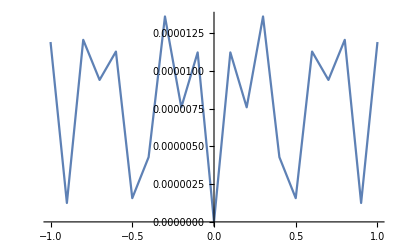

```mathematica
TablePlot[Abs[ρ[k]],{k,-1,1,0.1},PlotRange->All]
```

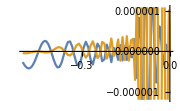

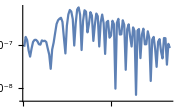

```mathematica
fr1=Fun[ρ[#]&,Line[{-.5,0.5}],100]
DCTPlot[fr1]
```

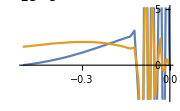

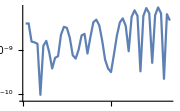

```mathematica
fr2=Fun[ρ[#]&,Line[{-.5,0}],50]
DCTPlot[fr2]
```

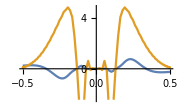

```mathematica
fr1'
```

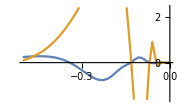

```mathematica
fr2'
```

```mathematica
dom
```

Line[{-8.8875,8.8875}]

## Cauchy Integral Reflection Coefficient

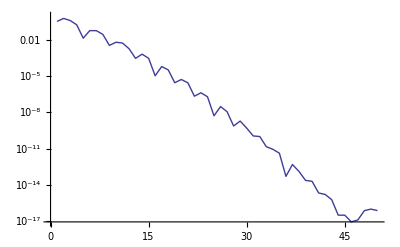
{3.71124×10^-16,-Graphics-}

```mathematica
q[x_]:=1.6Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Defocusing[];
LocatePolesmKdV[q,40];
H=ScatteringMatrixFinitemKdV[q,50,6];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];

SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^4);
Setrsamp[h];
Settimeflag[False];
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
```

```mathematica
up=I(ν+.0001);m=50;el=8;
f={Fun[ρ,Line[{-el,0}-up],2m],Fun[ρ,Line[{0,el}-up],2m],Fun[ρ,Line[{el,0}+up],m],Fun[ρ,Line[{0,-el}+up],m]};
```

```mathematica
mρ//Clear;
mρ[k_]:=mρ[k]=Piecewise[{{Cauchy[f,k], Im[k]< Im[up]}, {ρ[k], True}}];
SetScatteringData[aa,bb,mρ,LocatePolesmKdV[q,40]]
```

## Plotting: timestring outputs relevant computation times and region information

```mathematica
qSGkink=NotebookDirectory[]<>"qSGkink";
```

```mathematica
Get["qSGkink"];
```

```mathematica
qSG//Clear;
qSG[x_,t_]:=qSG[x,t]=SGAuto[x,t];
```

```mathematica
myacos[x_]:=Piecewise[{{ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[1,2]]]]>0},{2Pi-ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[1,2]]]]≤0}}];
```

```mathematica
xx=0.55;
tt=0.;
qSG[xx,tt]
timestring
```

{{0.596373+1.55937×10^-16 ⅈ,0.802707-4.01246×10^-16 ⅈ},{-0.802707+1.488×10^-16 ⅈ,0.596373+4.43152×10^-16 ⅈ}}

Region: 0 (0.55,0.) 1) Construct: 0.625  1) Solve: 0.40625  2) Construct: 0.828125  2) Solve: 0.234375

```mathematica
ans=qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]]
```

{{-0.288678+7.74487×10^-16 ⅈ,-0.957426+1.47583×10^-16 ⅈ},{-0.957426-6.1462×10^-16 ⅈ,0.288678-7.74487×10^-16 ⅈ}}

```mathematica
Cos[sol3[xx,tt]]-ans[[1,1]]
Sin[sol3[xx,tt]]-ans[[1,2]]
Sin[sol3[xx,tt]]-ans[[2,1]]
```

3.89166×10^-7-7.74487×10^-16 ⅈ

-1.1734×10^-7-1.47583×10^-16 ⅈ

-1.17338×10^-7+6.1462×10^-16 ⅈ

```mathematica
myacos[ans]-sol3[xx,tt]
```

-4.06471×10^-7

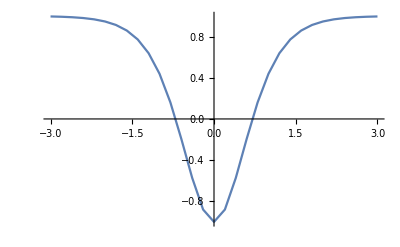

```mathematica
TablePlot[Cos[q[x]],{x,-3,3,0.2},PlotRange->All]
```

```mathematica
TablePlot[Re[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]],{x,-3,3,0.2},PlotRange->All]
```

$Aborted

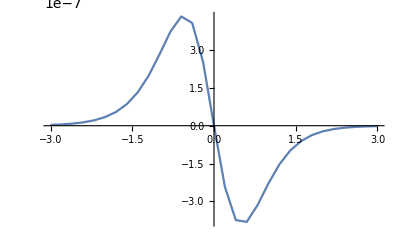

```mathematica
TablePlot[Abs[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]-Cos[q[x]]],{x,-3,3,0.2},PlotRange->All]
```

```mathematica
TablePlot[Im[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]],{x,-3,3,0.2},PlotRange->All]
```

```mathematica
xmin=-3;
xmax=3;
dx=0.2;
tmin=0;
tmax=2;
dt=0.2;
```

```mathematica
(*Plot cos of exact sol*)Manipulate[
LL=20;dd=0.2;
xx=Range[-LL,LL-dd,dd];
ListLinePlot[Cases[Table[{xx[[k]],Cos[Re[sol3[xx[[k]],tt]]]},{k,1,Length[xx]}],{x_,y_}/;xmin≤x≤xmax],PlotRange->{-1,1.0}],{tt,tmin,tmax,dt}]
```

```mathematica
Monitor[Table[qSG[x,tt],{x,xmin,xmax,dx},{tt,tmin,tmax,dt}],timestring];
Save[qSGkink,qSG];
```

```mathematica
(*plot computed cos*)
Manipulate[TablePlot[Re[1+2*qSG[x,tt][[1,2]]*qSG[x,tt][[2,1]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],{tt,tmin,tmax,dt}]
```

```mathematica
(*plot diff*)
Manipulate[
TablePlot[Re[1+2*qSG[x,tt][[1,2]]*qSG[x,tt][[2,1]]]-Cos[Re[sol3[x,tt]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],{tt,tmin,tmax,dt}]
```

```mathematica
(*Plot exact sol*)Manipulate[
LL=20;dd=0.2;
xx=Range[-LL,LL-dd,dd];
ListLinePlot[Cases[Table[{xx[[k]],Re[sol3[xx[[k]],tt]]},{k,1,Length[xx]}],{x_,y_}/;xmin≤x≤xmax],PlotRange->All],{tt,tmin,tmax,dt}]
```

```mathematica
Manipulate[TablePlot[Re[myacos[qSG[x,tt].{{1,0},{0,-1}}.Inverse[qSG[x,tt]]]],{x,xmin,xmax,dx},PlotRange->All],{tt,tmin,tmax,dt}]
```

```mathematica
Manipulate[TablePlot[Re[myacos[qSG[x,tt].{{1,0},{0,-1}}.Inverse[qSG[x,tt]]]-Re[sol3[x,tt]]],{x,xmin,xmax,dx},PlotRange->All],{tt,tmin,tmax,dt}]
```

```mathematica
(*solve linear eq, bad due to non periodicity*)Manipulate[
LL=20;dd=0.2;
xx=Range[-LL,LL-dd,dd];
qq[x_]:=q[x];
nq0=Table[qq[x],{x,-LL,LL-dd,dd}];(*even number of points*)
nqt0=Table[qt[x],{x,-LL,LL-dd,dd}];(*even number of points*)
w=Pi/LL*Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]];
nhq0=Fourier[nq0];
nhqt0=Fourier[nqt0];
(*nhqt=Quiet[nhq0*Exp[I/w*tt]*I*w/.Indeterminate->0.];*)
nhqt=(nhq0*Cos[Sqrt[1+w^2]*tt]+nhqt0/Sqrt[1+w^2]*Sin[Sqrt[1+w^2]*tt])/.Indeterminate->0.;
nqt=InverseFourier[nhqt];
ListLinePlot[Cases[Table[{xx[[k]],Re[nqt[[k]]]},{k,1,Length[nq0]}],{x_,y_}/;-LL≤x≤LL],PlotRange->All],{tt,tmin,tmax,dt}]
```

### Debug

```mathematica
(*test exact solution to the rhp for kink*)
```

```mathematica
z0=2I;c0=c[[1]];c0=4I;
AA[x_]=c0*Exp[I/2(z0-1/z0)*x];
BB[x_]=-cc[c0]*Exp[-I/2(cc[z0]-1/cc[z0])*x];
myrhs[z_,x_]:={{1+AA[x]/(z0-cc[z0])*(BB[x]/(1+AA[x]*BB[x]/(z0-cc[z0])^2))/(z-z0),(BB[x]/(1+AA[x]*BB[x]/(z0-cc[z0])^2))/(z-cc[z0])},
{(AA[x]/(1+AA[x]*BB[x]/(z0-cc[z0])^2))/(z-z0),1-BB[x]/(z0-cc[z0])*(AA[x]/(1+AA[x]*BB[x]/(z0-cc[z0])^2))/(z-cc[z0])}};
```

```mathematica
res1[z_,x_]=Simplify[myrhs[z,x]*(z-z0)];
res1[2I,x]//Simplify//MatrixForm
```

((4 ⅈ)/(1+ⅇ^(5 x/2)) | 0
(4 ⅈ ⅇ^(5 x/4))/(1+ⅇ^(5 x/2)) | 0)

```mathematica
res2[z_,x_]=myrhs[z,x].{{0,0},{c0*Exp[I/2(z0-1/z0)*x],0}};
res2[2I,x]//Simplify//MatrixForm
```

((4 ⅈ)/(1+ⅇ^(5 x/2)) | 0
(4 ⅈ ⅇ^(5 x/4))/(1+ⅇ^(5 x/2)) | 0)

```mathematica
res3[z_,x_]=FullSimplify[myrhs[z,x]*(z-cc[z0])];
res3[-2I,x]//Simplify//MatrixForm
```

(0 | 2 ⅈ Sech[(5 x)/4]
0 | 2 ⅈ (-1+Tanh[(5 x)/4]))

```mathematica
res4[z_,x_]=myrhs[z,x].{{0,-cc[c0]*Exp[-I/2(cc[z0]-1/cc[z0])*x]},{0,0}};
res4[-2I,x]//Simplify//MatrixForm
```

(0 | (4 ⅈ ⅇ^(5 x/4))/(1+ⅇ^(5 x/2))
0 | -(4 ⅈ)/(1+ⅇ^(5 x/2)))

```mathematica
ans2=myrhs[0,0.55].{{1,0},{0,-1}}.Inverse[myrhs[0,0.55]]
```

{{-0.288677+0. ⅈ,-0.957426+0. ⅈ},{-0.957426+0. ⅈ,0.288677+0. ⅈ}}

```mathematica
Cos[sol3[xx,tt]]-ans2[[1,1]]
Sin[sol3[xx,tt]]-ans2[[1,2]]
Sin[sol3[xx,tt]]-ans2[[2,1]]
```

-1.66533×10^-16+0. ⅈ

2.22045×10^-16+0. ⅈ

1.11022×10^-16+0. ⅈ